## Ricardian Trade

Consider the case of two countries, Jamaica and the Bahamas. Each countries produces (and demands) only two goods, sheep and marmalade. What we would like to know is under what conditions would it be beneficial for Jamaica and the Bahamas to trade.

We first need to initialize our toy model. For simplicity, we are going to insist that both countries have linear production possibility frontiers. At the extremes, Jamaica can produce either 2 flocks of sheep (and no marmalade) of 10 gallons of marmalade. (and no sheep).  Since their PPPs are linear, they are capable of producing every combination of sheep and marmalade that falls on the line that include the points (2,0) and (0,10). The Bahamas can produce either 8 sheep (and no marmalade) or 4 gallons of marmalade (and no sheep). 

We are going to start the problem in autarky - that is without trade. Each countries produces (and consumes) along its own production possibility frontier. I am arbitrarily going to decide (without loss of generality) that Jamaica produces 1 flock of sheep and 5 gallons of marmalade while the Bahamas produces 3 flocks of sheep and 2 gallons of marmalade. 

We can start the problem by sketching their production possibility frontiers.

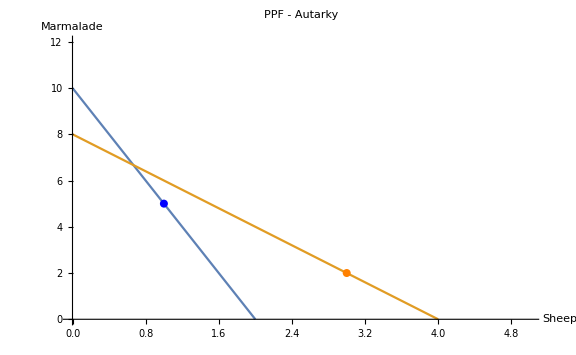

```mathematica
ClearAll["Global`*"]
jamaica[x_]:=10-5x; (* Equations from solving the function y=mx+b for the two sets of points *)
bahamas[x_]:=8-2x;
jamInit={1,5};bahInit ={3,2}; (* Autarky production points *)
points = {PointSize[.01],Blue,Point@jamInit, Orange,Point@bahInit};
ppf=Plot[{jamaica[x],bahamas[x]},{x,0,5}, PlotRange->{0,12},ImageSize->Large,AxesLabel->{"Sheep","Marmalade"},PlotLabel->"PPF - Autarky",Epilog->points]
```

### Absolute Advantage

A country is said to have an absolute advantage if it can produce more of a given good than another countries. We can look at the extremes to figure out which country is capable of outproduce the other country and for what good.

### Comparative Advantage

J=10/2=5. Every new flock of sheep costs 5 gallons of marmalade.
B=8/4=2. Every new flock of sheep costs 2 gallons of marmalade.

Sheep production is relatively cheaper for the Bahamas than for Jamaica where cost is defined in terms of a countries own capacity.

### Trade

A trade agreement occurs when two countries get together and say “I will give you so much of good x in exchange for so much of good y”. The amount of good x that is costs to receive a unit of good y is called the relative price. How do countries agree on a relative price?

Well we cannot exactly predict the relative price, but we know that the comparative advantages of the two countries effective create bounds on possible trade agreements.  If the relative price is too low, then one country may as well produce domestically. If the relative price is too high, the other country would be better off producing domestically. This seems odd, but if we invert the relative price to form the quantity of good y in exchange for a unit of good x, then you can easily see that at too high an original relative prices, the effective relative price for the other good drops. This may seem odd at first, but the simulation below should enforce how comparative advantages create minimum and maximum relative prices for trade agreements.

```mathematica
Manipulate[
newJam={0,10} + {q,-rp*q};
newBah={4,0} + {-q,rp*q};
newPoints = {Blue, Point@newJam, Orange,Point@ newBah};
Plot[{jamaica[x],bahamas[x]},{x,0,5}, PlotRange->{0,12},ImageSize->Large,AxesLabel->{"Sheep","Marmalade"},PlotLabel->"PPF - After Trade",Epilog->{PointSize[.0075],points, newPoints,Blue, Dotted,Arrowheads[Medium], Arrow@{jamInit, newJam},Orange,Arrow@{bahInit,newBah}}],
{{rp, 0,"Relative price (Sheep for marmalade)"},-10,10},{{q,1,"Quantity"},0,5}]
```